```mathematica
(*********坐标系*********)
f1={Graphics3D[{
{Arrowheads[0.02],Arrow[{{0,0,0},{1.3,0,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,0},{0,1.5,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,0},{0,0,1.3}}]}
},
Boxed->False,AspectRatio->Automatic
]
};
(*********空间区域*********)
f2={
Plot3D[x*y/(x^2+y^2),{x,-1,1},{y,-1,1},
Mesh->10,MeshFunctions->{#3&},MeshStyle->{White,Opacity[0.5]},
PlotPoints->50,
PlotStyle->{Opacity[0.8]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
]
};
(*********空间曲线、点*********)
f3={

};
(*********曲面+投影区域*********)
f4={

};
(*********文字标记*********)
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
f5=Graphics3D[{
Text[Style[x,tF,Large,Italic],{1.4,0,0.1}],
Text[Style["y",tF,Large,Italic],{0,1.5,0.2}],
Text[Style["z",tF,Large,Italic],{0,0.1,1.3}],
Text[Style["0.5",tF,Medium],{0,0.15,0.6}],
Text[Style[O,tF,Italic],{0,-0.1,0.04}]
}];
Show[f1,f2,f3,f4,f5,ViewPoint->{2,-2,2}]
```

-Graphics3D-

```mathematica
Show[f1,f2,f3,f4,f5,ViewPoint->{2,3,3}]
```

-Graphics3D-

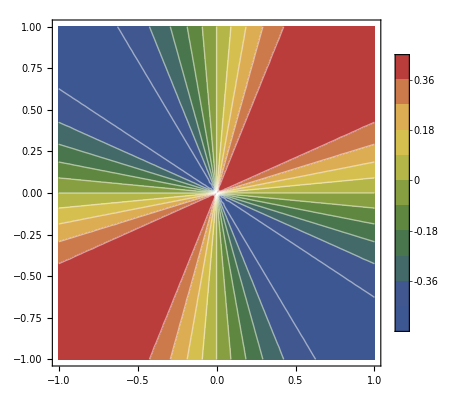

```mathematica
ContourPlot[x*y/(x^2+y^2),{x,-1,1},{y,-1,1},PlotLegends->Automatic,
ColorFunction->"DarkRainbow",ContourStyle->{White},Contours->10]
```

```mathematica
(*********字体设置*********)
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(*********坐标系*********)
f1={Graphics3D[{
{Arrowheads[0.02],Arrow[{{0,0,0},{3.3,0,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,0},{0,3.5,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,0},{0,0,2.6}}]},
Text[Style["x",tF,Italic],{3.4,0,0.1}],
Text[Style["y",tF,Italic],{0,3.5,0.2}],
Text[Style["z",tF,Italic],{0,0.2,2.6}],
Text[Style[O,tF,Italic],{-0.1,-0.1,0.04}]
},
Boxed->False,AspectRatio->Automatic
]
};
(*********空间区域*********)
f2={
Plot3D[(x^2-y^2)/(x^2+y^2),{x,-3,3},{y,-3,3},
Mesh->None,
PlotPoints->50,
PlotStyle->{Opacity[0.6]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
]
};
(*********空间曲线、点*********)
f3={
Graphics3D[{
{Arrowheads[0.03],Blue,Thick,Arrow[{{3,0,1},{0,0,1}}]},
{Arrowheads[0.03],Blue,Thick,Arrow[{{-3,0,1},{0,0,1}}]},
{Arrowheads[0.03],Red,Thick,Arrow[{{0,-3,-1},{0,0,-1}}]},
{Arrowheads[0.03],Red,Thick,Arrow[{{0,3,-1},{0,0,-1}}]},
{PointSize[Large],Point[{0,0,1}]},
{PointSize[Large],Point[{0,0,-1}]}
}]
};
(*********曲面+投影区域*********)
f4={

};
(*********文字标记*********)
f5=Graphics3D[{
Text[Style["1",tF,Blue],{0,0.25,1.2}],
Text[Style["-1",tF,Red],{0.3,-0.25,-1.2}]
}];
Show[f1,f2,f3,f4,f5,ViewPoint->{2,-2,2}]
```

-Graphics3D-

```mathematica
(*********字体设置*********)
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(*********坐标系*********)
f1={Graphics3D[{
{Arrowheads[0.02],Arrow[{{0,0,0},{3.3,0,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,0},{0,3.5,0}}]},
{Arrowheads[0.02],Arrow[{{0,0,0},{0,0,2.6}}]},
Text[Style["x",tF,Italic],{3.4,0,0.1}],
Text[Style["y",tF,Italic],{0,3.5,0.2}],
Text[Style["z",tF,Italic],{0,0.2,2.6}],
Text[Style[O,tF,Italic],{-0.1,-0.2,0.04}]
},
Boxed->False,AspectRatio->Automatic
]
};
(*********空间区域*********)
f2={
Plot3D[(x^2y)/(x^2+y^2),{x,-3,3},{y,-3,3},
Mesh->10,MeshFunctions->{#3&},MeshStyle->{White,Opacity[0.5]},
PlotPoints->50,
PlotStyle->{Opacity[0.8]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow"
]
};
(*********空间曲线、点*********)
f3={

};
(*********曲面+投影区域*********)
f4={

};
(*********文字标记*********)
f5=Graphics3D[{

}];
Show[f1,f2,f3,f4,f5,ViewPoint->{2,-2,2}]
```

-Graphics3D-

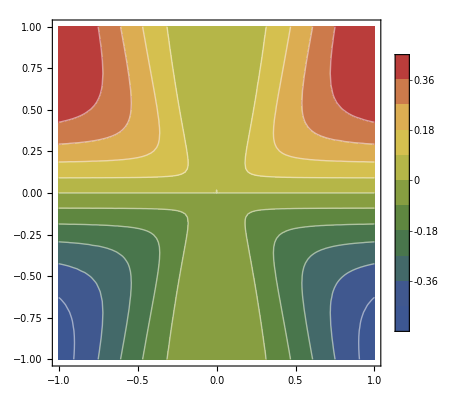

```mathematica
ContourPlot[(x^2y)/(x^2+y^2),{x,-1,1},{y,-1,1},PlotLegends->Automatic,
ColorFunction->"DarkRainbow",ContourStyle->{White},Contours->10]
```

```mathematica
Plot3D[x*y^2/(x^2+y^4),{x,-1,1},{y,-1,1},
Mesh->10,MeshFunctions->{#3&},MeshStyle->{White,Opacity[0.5]},
PlotPoints->20,(*120*)
PlotStyle->{Opacity[0.8]},
BoundaryStyle->None,
ColorFunction->"DarkRainbow",
Boxed->False
]
```

-Graphics3D-

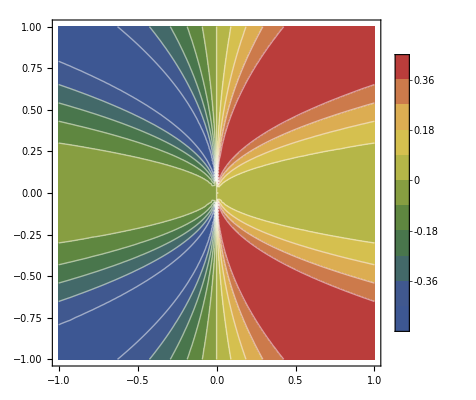

```mathematica
ContourPlot[(x*y^2)/(x^2+y^4),{x,-1,1},{y,-1,1},PlotLegends->Automatic,
ColorFunction->"DarkRainbow",ContourStyle->{White},Contours->10]
```